sWLC from Li et at, 2020
Re-viewing calculation
Lossless first, then lossy

```mathematica
(*poles of transfer functions, shared by signal and noise*)
κ=1;
γR=1;
Manipulate[ListPlot[{{Re[(-I γR+I(γR^2+4(χ^2-κ^2))^(1/2))/2],Im[(-I γR+I(γR^2+4(χ^2-κ^2))^(1/2))/2]},{Re[(-I γR-I(γR^2+4(χ^2-κ^2))^(1/2))/2],Im[(-I γR-I(γR^2+4(χ^2-κ^2))^(1/2))/2]}},PlotRange->{{-2,2},{-3,2}},AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium],PlotLabel->StringForm["poles of lossless transfer function\nunstable when Im[Ω]≥0\nχ/κ=``",χ/κ]],{{χ,0},0,2κ,0.1}]
```

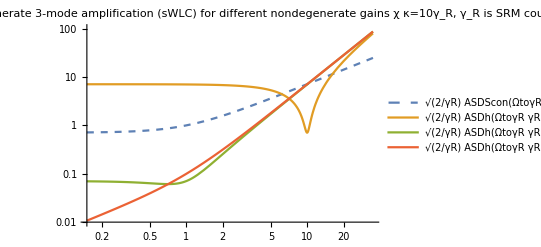
-Graphics-angular freq, Ω/γ_R / [1/γ_R]Hz (log scale)strain sensitivity (NSR), ((2 SuperscriptBox[α, 2] SubscriptBox[S, h])/γ_R)^(1/2)
/ [α/γ_R^(1/2)]Hz^(-1/2) (log scale)

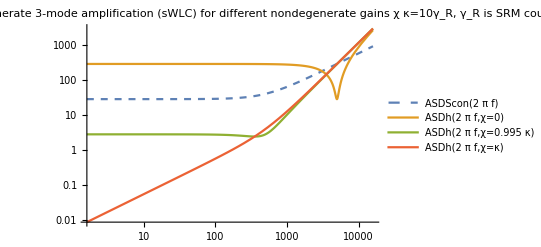
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR), (α^2S_h)^(1/2)
/ [α]Hz^(-1/2) (log scale)

```mathematica
(*sensitivity curve, using values from Fig.4-5 in Li et al, 2020
they choose to plot ((2 α^2 Subscript[S, h])/Subscript[γ, R])^(1/2)*)
Clear[α,χ,κ,γR];
α=1;
γR=2π 500 (*Hz*);
κ=10γR;
Sh[Ω_,χ_]:=((Ω^2+χ^2-κ^2)^2+Ω^2 γR^2)/(4 α^2 κ^2 γR)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
ASDScon[Ω_]:=((Ω^2+γR^2)/(4 α^2 γR) )^(1/2)(*given*)
Labeled[LogLogPlot[{
(2/γR)^(1/2)ASDScon[ΩtoγR γR],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0.995κ],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=κ]},{ΩtoγR,0.15,35},ImageSize->400,PlotRange->{0.01,100},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"angular freq, Ω/γ_R / [1/γ_R]Hz (log scale)","strain sensitivity (NSR), ((2 SuperscriptBox[α, 2] SubscriptBox[S, h])/γ_R)^(1/2)\n/ [α/γ_R^(1/2)]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
(*y-axis looks all wrong because we have scaled to α*)
Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.995κ],
ASDh[2π f,χ=κ]},{f,10/(2π),10^5/(2π)},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR), (α^2S_h)^(1/2)\n/ [α]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

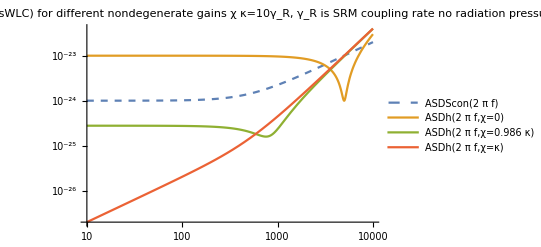
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR), S_h^(1/2)
/ Hz^(-1/2) (log scale)

```mathematica
(*want to plot Sh^(1/2) against f using real values, to compare to sensitivity target
(recreating Fig.5 in Li et al, 2020 also requires radiation pressure noise, not yet derived)
This requires using the correct Subscript[α, GW] scale*)
Clear[α,χ,κ,γR];
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
Larm=4 10^3(*m*);
Pcirc=3 10^6(*J/s*);
λ0=2 10^-6(*m*);
ω0=2π c/λ0;
(*value in Li et al doesn't make sense dimensionally, using Korobko et al 2019 instead
α=((2Pcirc ℏ ω0)/(c Larm))^(1/2);*)
α=((2Pcirc Larm ω0)/(ℏ c))^(1/2);
γR=2π 500 (*Hz*);
κ=10γR;
Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.986κ],
ASDh[2π f,χ=κ]},{f,10,10^4},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR), S_h^(1/2)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

```mathematica
(*(*integrated lossless sensitivity*)
(4 α1^2 κ1^2 γR1)/(2π)Integrate[1/((Ω^2+χ1^2-κ1^2)^2+γR1^2 Ω^2),{Ω,0,∞},Assumptions->{χ1>0,κ1>0,γR1>0}]*)
```

Lossy sensitivity, adding loss terms to each mode, assuming each noise is quantum with uncorrelated vacuum bath

True

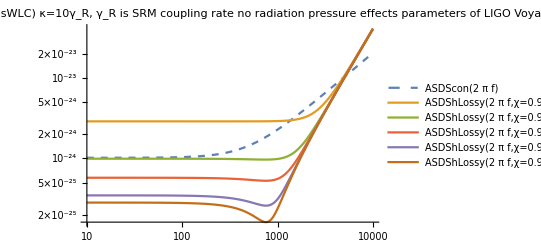
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR), S_h^(1/2)
/ Hz^(-1/2) (log scale)

```mathematica
Clear[γa,γb,γc,γbtot]
ShLossy[Ω_,χ_]:=1/(4 α^2 κ^2 γR(γc^2+Ω^2))(
((γbtot-2γR)(γa γc-Ω^2)-(γa+γc)Ω^2+κ^2 γc-χ^2 γa)^2
+Ω^2(χ^2-κ^2-(γbtot-2γR)(γa+γc)-γa γc+Ω^2)^2
+4γR γa κ^2(γc^2+Ω^2)
+4γR γb(γa^2+Ω^2)(γc^2+Ω^2)
+4γR γc χ^2(γa^2+Ω^2))
ASDShLossy[Ω_,χ_,lossRatio_]:=(ShLossy[Ω,χ]^(1/2))/.{γa->(lossRatio γR)/(1-lossRatio),γb->(lossRatio γR)/(1-lossRatio),γc->(lossRatio γR)/(1-lossRatio),γbtot->γR+(lossRatio γR)/(1-lossRatio)}
(*Checking that lossy expression can be recovered*)
losslessAsmps={γa->0,γb->0,γc->0,γbtot->γR};
((ShLossy[Ω,χ]/.losslessAsmps)==Sh[Ω,χ])//Simplify
(*Plotting*)
Labeled[LogLogPlot[{
ASDScon[2π f],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.5],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.1],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.03],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.005],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0]},{f,10,10^4},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy stable nondegenerate 3-mode amplification (sWLC)\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager\nconventional detector is lossless",PlotStyle->{Dashed,,,,,}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR), S_h^(1/2)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

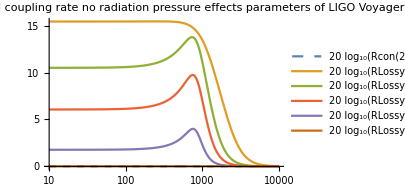
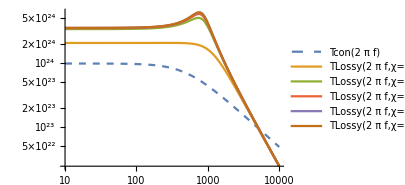
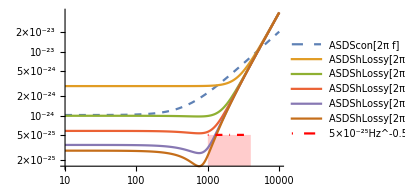
-Graphics-shot noise transfer function,
|R| / dB (20log10)
-Graphics-signal transfer function,
|T| / [?] (log scale)
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR)
/ Hz^-0.5 (log scale)

```mathematica
(*plotting signal and noise transfer functions separetely
Subscript[S, h]=(|R|^2+...+|Rc|^2)/(|T|^2), plot Subscript[S, h]^(1/2)=((|R|^2+...+|Rc|^2)^(1/2))/(|T|). Here, plot |T| and (|R|^2+...+|Rc|^2)^(1/2)*)
Clear[γa,γb,γc,γbtot]
TLossy[Ω_,χ_,lossRatio_]:=Abs[((-2α κ γR^(1/2))/(γa-I Ω))/(γbtot-I Ω+κ^2/(γa-I Ω)-χ^2/(γc-I Ω))]/.{γa->(lossRatio γR)/(1-lossRatio),γb->(lossRatio γR)/(1-lossRatio),γc->(lossRatio γR)/(1-lossRatio),γbtot->γR+(lossRatio γR)/(1-lossRatio)}
RLossy[Ω_,χ_,lossRatio_]:=((Abs[γbtot-2γR-I Ω+κ^2/(γa-I Ω)-χ^2/(γc-I Ω)]^2+Abs[(-2(γR γa)^(1/2)κ)/(γa-I Ω)]^2+Abs[-2(γR γb)^(1/2)]^2+Abs[(2(γR γc)^(1/2)χ)/(γc-I Ω)]^2)/(Abs[γbtot-I Ω+κ^2/(γa-I Ω)-χ^2/(γc-I Ω)]^2))^(1/2)/.{γa->(lossRatio γR)/(1-lossRatio),γb->(lossRatio γR)/(1-lossRatio),γc->(lossRatio γR)/(1-lossRatio),γbtot->γR+(lossRatio γR)/(1-lossRatio)}
Tcon[Ω_]:=Abs[(-2I α γR^(1/2))/(Ω+I γR) ](*given*)
Rcon[Ω_]:=Abs[(Ω-I γR)/(Ω+I γR) ]
(*Plotting*)
p1=Labeled[LogLinearPlot[{
20Log10[Rcon[2π f]],
20Log10[RLossy[2π f,χ=0.986κ,lossRatio=0.5]],
20Log10[RLossy[2π f,χ=0.986κ,lossRatio=0.1]],
20Log10[RLossy[2π f,χ=0.986κ,lossRatio=0.03]],
20Log10[RLossy[2π f,χ=0.986κ,lossRatio=0.005]],
20Log10[RLossy[2π f,χ=0.986κ,lossRatio=0]]},{f,10,10^4},ImageSize->300,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager\nconventional detector is lossless",PlotStyle->{Dashed,,,,,},
ImagePadding->{{50,10},{0,0}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All}],"shot noise transfer function,\n|R| / dB (20log10)",Left,RotateLabel->True,LabelStyle->Directive[10]];
p2=Labeled[LogLogPlot[{
Tcon[2π f],
TLossy[2π f,χ=0.986κ,lossRatio=0.5],
TLossy[2π f,χ=0.986κ,lossRatio=0.1],
TLossy[2π f,χ=0.986κ,lossRatio=0.03],
TLossy[2π f,χ=0.986κ,lossRatio=0.005],
TLossy[2π f,χ=0.986κ,lossRatio=0]},{f,10,10^4},ImageSize->300,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotStyle->{Dashed,,,,,},ImagePadding->{{50,10},{0,5}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All}],"signal transfer function,\n|T| / [?] (log scale)",Left,RotateLabel->True,LabelStyle->Directive[10]];
p3=Labeled[LogLogPlot[{
ASDScon[2π f],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.5],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.1],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.03],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0.005],
ASDShLossy[2π f,χ=0.986κ,lossRatio=0],
If[10^3<#<4 10^3,5 10^-25,Null]&[f]},{f,10,10^4},ImageSize->300,ImagePadding->{{50,10},{10,5}},PlotLegends->LineLegend[{"ASDScon[2π f]","ASDShLossy[2π f,χ=0.986κ,lossRatio=0.5]","ASDShLossy[2π f,χ=0.986κ,lossRatio=0.1]","ASDShLossy[2π f,χ=0.986κ,lossRatio=0.03]","ASDShLossy[2π f,χ=0.986κ,lossRatio=0.005]","ASDShLossy[2π f,χ=0.986κ,lossRatio=0]", "5×10^-25Hz^-0.5 target for 1–4 kHz"},LabelStyle->Directive[10]],PlotStyle->{Dashed,,,,,,Directive[DotDashed,Red]},PlotRange->{{10,10^4},All},Filling->{7->Bottom}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]];
Column[{p1,p2,p3},Spacings->0]
```

lossless: {{Ω→-500 ⅈ π-ⅈ √(250000 π^2-κ^2+χ^2)},{Ω→-500 ⅈ π+ⅈ √(250000 π^2-κ^2+χ^2)}}

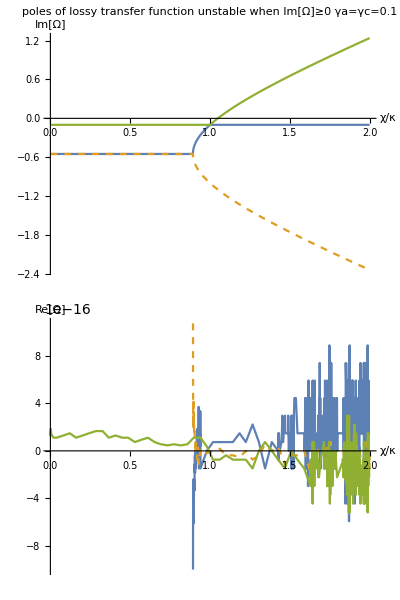

```mathematica
(*Checking stability*)
Clear[χ,κ,γbtot,γa,γc]
denominator=γbtot-I Ω+κ^2/(γa-I Ω)-χ^2/(γc-I Ω);
(*additional poles at γa,γc*)
Print["lossless: ",Solve[(denominator/.losslessAsmps)==0,Ω]]
sol=Simplify[Solve[denominator==0,Ω],Assumptions->{κ>0,χ>0,γa>0,γbtot>0,γc>0}];
κ=1;
γbtot=1;
γa=0.1;
γc=0.1;
(*Print["lossy: ",sol]*)
p1=Plot[{Im[Ω/.sol[[1]]],Im[Ω/.sol[[2]]],Im[Ω/.sol[[3]]]},{χ,0,2κ},AxesLabel->{"χ/κ","Im[Ω]"},PlotLabel->"poles of lossy transfer function\nunstable when Im[Ω]≥0\nγa=γc=0.1",PlotStyle->{,Dashed,},
ImagePadding->{{50,20},{10,0}},ImageSize->300];
p2=Plot[{Re[Ω/.sol[[1]]],Re[Ω/.sol[[2]]],Re[Ω/.sol[[3]]]},{χ,0,2κ},AxesLabel->{"χ/κ","Re[Ω]"},PlotStyle->{,Dashed,},
ImagePadding->{{50,20},{10,20}},ImageSize->300];
Column[{p1,p2},Spacings->0]
```

```mathematica
(*https://flatuicolors.com/palette/us*)
(*DarkAmerican={RGBColor["#0984e3"],RGBColor["#00b894"],RGBColor["#d63031"],RGBColor["#e84393"],RGBColor["#6c5ce7"],RGBColor["#e17055"],RGBColor["#00cec9"],RGBColor["#fdcb6e"]};
LightAmerican={RGBColor["#74b9ff"],RGBColor["#55efc4"],RGBColor["#ff7675"],RGBColor["#fd79a8"],RGBColor["#a29bfe"],RGBColor["#fab1a0"],RGBColor["#81ecec"],RGBColor["#ffeaa7"]};
American=Join[DarkAmerican,LightAmerican];*)
```

```mathematica
(*introducing photodetector (PD) loss, Subscript[R, PD] is the reflectivity of the lossless beam-splitter before the PD*)
α=((2Pcirc Larm ω0)/(ℏ c))^(1/2);
γR=2π 500 (*Hz*);
κ=10γR;
Clear[γa,γb,γc,γbtot]
γa[lossRatio_]:=(lossRatio γR)/(1-lossRatio)
γb[lossRatio_]:=(lossRatio γR)/(1-lossRatio)
γc[lossRatio_]:=(lossRatio γR)/(1-lossRatio)
γbtot[lossRatio_]:=γR+(lossRatio γR)/(1-lossRatio)
TPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=(1-Rpd)^(1/2)Abs[((-2α κ γR^(1/2))/(γa[lossRatio]-I Ω))/(γbtot[lossRatio]-I Ω+κ^2/(γa[lossRatio]-I Ω)-χ^2/(γc[lossRatio]-I Ω))]
RPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=((1-Rpd)((
Abs[γbtot[lossRatio]-2γR-I Ω+κ^2/(γa[lossRatio]-I Ω)-χ^2/(γc[lossRatio]-I Ω)]^2
+Abs[(-2(γR γa[lossRatio])^(1/2)κ)/(γa[lossRatio]-I Ω)]^2
+Abs[-2(γR γb[lossRatio])^(1/2)]^2
+Abs[(2(γR γc[lossRatio])^(1/2)χ)/(γc[lossRatio]-I Ω)]^2)/Abs[γbtot[lossRatio]-I Ω+κ^2/(γa[lossRatio]-I Ω)-χ^2/(γc[lossRatio]-I Ω)]^2)+Rpd)^(1/2)
ASDhPDLossy[Ω_,χ_,lossRatio_,Rpd_]:=(1/((γc[lossRatio]^2+Ω^2)4 α^2 κ^2 γR)(
((γbtot[lossRatio]-2γR)(γa[lossRatio] γc[lossRatio]-Ω^2)-(γa[lossRatio]+γc[lossRatio])Ω^2+κ^2 γc[lossRatio]-χ^2 γa[lossRatio])^2
+Ω^2(χ^2-κ^2-(γbtot[lossRatio]-2γR)(γa[lossRatio]+γc[lossRatio])-γa [lossRatio]γc[lossRatio]+Ω^2)^2
+4γR γa[lossRatio] κ^2(γc[lossRatio]^2+Ω^2)
+4γR γb[lossRatio](γa[lossRatio]^2+Ω^2)(γc[lossRatio]^2+Ω^2)
+4γR γc[lossRatio] χ^2(γa[lossRatio]^2+Ω^2)
+Rpd/(1-Rpd)((γbtot[lossRatio](γa[lossRatio] γc[lossRatio]-Ω^2)-(γa[lossRatio]+γc[lossRatio])Ω^2+κ^2 γc[lossRatio]-χ^2 γa[lossRatio])^2
+Ω^2(χ^2-κ^2-γbtot[lossRatio](γa[lossRatio]+γc[lossRatio])-γa [lossRatio]γc[lossRatio]+Ω^2)^2)))^(1/2)
```

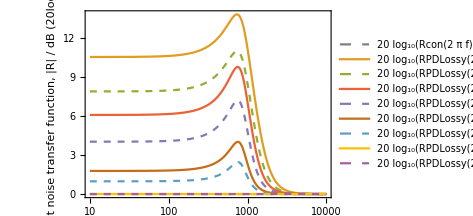
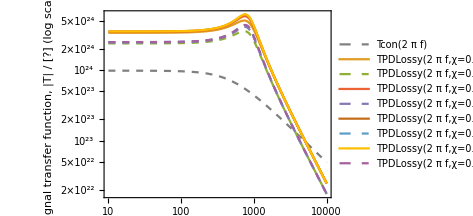
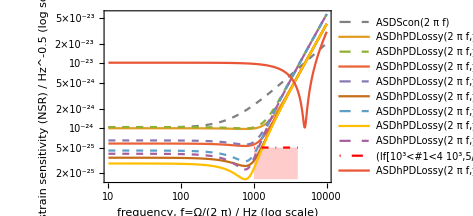

```mathematica
(*Plotting*)
p1=LogLinearPlot[{
20Log10[Rcon[2π f]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0.1,Rpd=0]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0.1,Rpd=0.5]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0.03,Rpd=0]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0.03,Rpd=0.5]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0.005,Rpd=0]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0.005,Rpd=0.5]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0,Rpd=0]],
20Log10[RPDLossy[2π f,χ=0.986κ,lossRatio=0,Rpd=0.5]]},{f,10,10^4},ImageSize->350,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],
ImagePadding->{{90,10},{1,115}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->{Directive[Dashed,Gray],,Dashed,,Dashed,,Dashed,,Dashed},Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,"lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager\nconventional detector is lossless\nwith PD loss"}}];
p2=LogLogPlot[{
Tcon[2π f],
TPDLossy[2π f,χ=0.986κ,lossRatio=0.1,Rpd=0],
TPDLossy[2π f,χ=0.986κ,lossRatio=0.1,Rpd=0.5],
TPDLossy[2π f,χ=0.986κ,lossRatio=0.03,Rpd=0],
TPDLossy[2π f,χ=0.986κ,lossRatio=0.03,Rpd=0.5],
TPDLossy[2π f,χ=0.986κ,lossRatio=0.005,Rpd=0],
TPDLossy[2π f,χ=0.986κ,lossRatio=0.005,Rpd=0.5],
TPDLossy[2π f,χ=0.986κ,lossRatio=0,Rpd=0],
TPDLossy[2π f,χ=0.986κ,lossRatio=0,Rpd=0.5]},{f,10,10^4},ImageSize->350,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],ImagePadding->{{90,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->{Directive[Dashed,Gray],,Dashed,,Dashed,,Dashed,,Dashed},Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[{
ASDScon[2π f],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0.1,Rpd=0],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0.1,Rpd=0.5],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0.03,Rpd=0],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0.03,Rpd=0.5],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0.005,Rpd=0],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0.005,Rpd=0.5],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0,Rpd=0],
ASDhPDLossy[2π f,χ=0.986κ,lossRatio=0,Rpd=0.5],
If[10^3<#<4 10^3,5 10^-25,Null]&[f],
ASDhPDLossy[2π f,χ=0,lossRatio=0,Rpd=0]
},{f,10,10^4},ImageSize->350,ImagePadding->{{90,10},{50,1}},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotStyle->{Directive[Dashed,Gray],,Dashed,,Dashed,,Dashed,,Dashed,Directive[DotDashed,Red],},PlotRange->{{10,10^4},All},Filling->{10->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0]
```

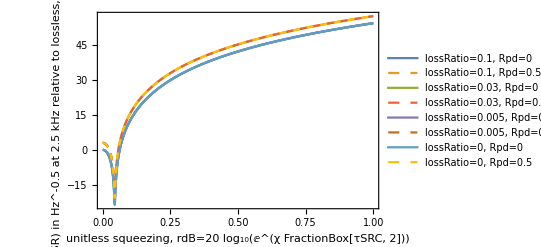

rdB→0.0441125

To a tolerance of 0.00001, the optimum χ is on threshold: False

{27207.,31415.9,0.866025}

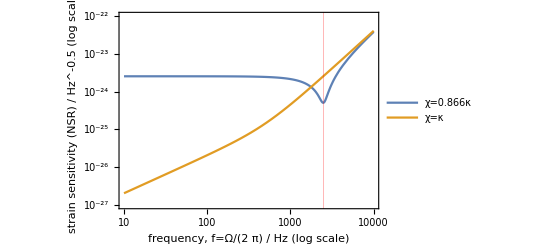

```mathematica
(*sensitivity at 2.5 kHz versus squeezer parameter, like deg.int.sqz. plot*)
fProbe=2.5 10^3(*Hz*);
sensRef = ASDhPDLossy[2π fProbe,0,lossRatio=0,Rpd=0];(*sensitivity reference: lossless, no squeezing, i.e. conventional*)
Lse=56(*m, using aLIGO value until figure out LIGO Voyager*);
τSE=(2 Lse)/c; (*round-trip*)
Plot[{
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.1,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.1,Rpd=0.5]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.03,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.03,Rpd=0.5]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.005,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0.005,Rpd=0.5]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0,Rpd=0]/sensRef],
20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0,Rpd=0.5]/sensRef]},{rdB,0,1},PlotRange->All,PlotLegends->LineLegend[{"lossRatio=0.1, Rpd=0","lossRatio=0.1, Rpd=0.5","lossRatio=0.03, Rpd=0","lossRatio=0.03, Rpd=0.5","lossRatio=0.005, Rpd=0","lossRatio=0.005, Rpd=0.5","lossRatio=0, Rpd=0","lossRatio=0, Rpd=0.5"},LabelStyle->Directive[10]],PlotStyle->{,Dashed,,Dashed,,Dashed,,Dashed},Frame->True,FrameLabel->{{StringForm["strain sensitivity (NSR) in Hz^-0.5 at `` kHz\nrelative to lossless, no squeezing value / dB",fProbe/10^3],},{"unitless squeezing, rdB=20 log_10(ⅇ^(χ FractionBox[τSRC, 2]))","lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager w 56m SRC\nconventional detector is lossless\nwith PD loss"}}]
(*showing that minimum is indeed χ=kout*)
thresholdrdB = N[Minimize[{20Log10[ASDhPDLossy[2π fProbe,2/τSE Log[10^(rdB/20)],lossRatio=0,Rpd=0]/sensRef],rdB>0},{rdB}][[2]][[1]]]
thresholdχ=2/τSE Log[10^(rdB/20)]/.thresholdrdB;
tolerance=N[10^-5];
Print[StringForm["To a tolerance of ``, the optimum χ is on threshold: ",tolerance],Abs[(thresholdχ-κ)/κ]<tolerance]
{thresholdχ,N[κ],thresholdχ/N[κ]}
(*Manipulate[LogLogPlot[ASDhPDLossy[2π f,χ=rat κ,lossRatio=0,Rpd=0],{f,10,10^4},PlotRange->{10^-27,10^-22},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2 π) / Hz (log scale)",StringForm["above process optimises for sensitivity at `` kHz\nnot for overall bandwidth\nχ/κ=``",fProbe/10^3,χ/κ]}},GridLines->{{{fProbe,Red}},None}],{{rat,thresholdχ/N[κ],"χ/κ"},0,2}]*)
LogLogPlot[{
ASDhPDLossy[2π f,χ=thresholdχ/N[κ] κ,lossRatio=0,Rpd=0],
ASDhPDLossy[2π f,χ= κ,lossRatio=0,Rpd=0]},{f,10,10^4},PlotRange->{10^-27,10^-22},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",StringForm["sWLC - lossless\nabove process optimises for sensitivity at `` kHz\nnot for overall bandwidth",fProbe/10^3]}},GridLines->{{{fProbe,Red}},None},PlotLegends->{StringForm["χ=``κ",NumberForm[thresholdχ/N[κ],4]],"χ=κ"}]
```

```mathematica
(*semi-automated plotting*)
(*separating losses and making transmittivities inputs*)
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
τRoundTripArm=(2 Larm)/c;
γa[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
(*Assuming LIGO Voyager's Subscript[T, SRM] was used for γR
this is different to above for the threshold plots where I assumed the LIGO value of 56m was used for Subscript[L, SRC]*)
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];(*Subscript[γ, R]=-1/(2 τRoundTripSRC)Log[1-Tsrm]*)
γb[Tlb_]:=-1/(2 τRoundTripSRC)Log[1-Tlb]
γbtot[Tlb_]:=γR+γb[Tlb]
(*assuming that c mode is also in SRC, e.g. non-degenerate internal squeezing*)
γc[Tlc_]:=-1/(2 τRoundTripSRC)Log[1-Tlc]
TsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_]:=(1-Rpd)^(1/2)Abs[((-2α κ γR^(1/2))/(γa[Tla]-I Ω))/(γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc]-I Ω))]
RsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_]:=((1-Rpd)((
Abs[γbtot[Tlb]-2γR-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc]-I Ω)]^2
+Abs[(-2(γR γa[Tla])^(1/2)κ)/(γa[Tla]-I Ω)]^2
+Abs[-2(γR γb[Tlb])^(1/2)]^2
+Abs[(2(γR γc[Tlc])^(1/2)χ)/(γc[Tlc]-I Ω)]^2)/Abs[γbtot[Tlb]-I Ω+κ^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc]-I Ω)]^2)+Rpd)^(1/2)
ASDShsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_]:=(1/((γc[Tlc]^2+Ω^2)4 α^2 κ^2 γR)(
((γbtot[Tlb]-2γR)(γa[Tla] γc[Tlc]-Ω^2)-(γa[Tla]+γc[Tlc])Ω^2+κ^2 γc[Tlc]-χ^2 γa[Tla])^2
+Ω^2(χ^2-κ^2-(γbtot[Tlb]-2γR)(γa[Tla]+γc[Tlc])-γa [Tla]γc[Tlc]+Ω^2)^2
+4γR γa[Tla] κ^2(γc[Tlc]^2+Ω^2)
+4γR γb[Tlb](γa[Tla]^2+Ω^2)(γc[Tlc]^2+Ω^2)
+4γR γc[Tlc] χ^2(γa[Tla]^2+Ω^2)
+Rpd/(1-Rpd)((γbtot[Tlb](γa[Tla] γc[Tlc]-Ω^2)-(γa[Tla]+γc[Tlc])Ω^2+κ^2 γc[Tlc]-χ^2 γa[Tla])^2
+Ω^2(χ^2-κ^2-γbtot[Tlb](γa[Tla]+γc[Tlc])-γa [Tla]γc[Tlc]+Ω^2)^2)))^(1/2)

(*values are: χ, Tla, Tlb, Tlc, Rpd*)
unpackRsWLC[Ω_,vals_]:=RsWLC[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]]]
unpackTsWLC[Ω_,vals_]:=TsWLC[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]]]
unpackASDShsWLC[Ω_,vals_]:=ASDShsWLC[Ω,vals[[1]],vals[[2]],vals[[3]],vals[[4]],vals[[5]]]
labeller1[vals_]:=(
paddedStrings=StringPadRight[{ToString[N[vals[[1]]/κ]],ToString[vals[[2]]],ToString[vals[[3]]],ToString[vals[[4]]],ToString[vals[[5]]]},4];
Style[StringForm["χ/κ=``; T_(l, a)=``, T_(l, b)=``, T_(l, c)=``, R_PD=``",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],FontFamily->"Monospace"]
(*search for mono-spaced fonts in: $FontFamilies*)
)

(*plotting*)
plotsWLC[valsList_,plotLabel_:"optical stable WLC",plotStyle_:{}]:=(
p1=LogLinearPlot[Evaluate[Join[
{20Log10[Rcon[2π f]]},
Table[20Log10[unpackRsWLC[2π f,valsList[[i]]]],{i,1,Length[valsList]}]]]
,{f,10,10^4},ImageSize->350,PlotLegends->LineLegend[Join[{"lossless conventional"},Table[labeller1[valsList[[i]]],{i,1,Length[valsList]}]],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{90,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->If[plotStyle=={},Join[{Directive[Gray,DotDashed]},Table[,{n,1,Length[valsList]}]],Join[{Directive[Gray,DotDashed]},plotStyle]],Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,plotLabel}}];
p2=LogLogPlot[Evaluate[Join[
{Tcon[2π f]},
Table[unpackTsWLC[2π f,valsList[[i]]],{i,1,Length[valsList]}]]],{f,10,10^4},ImageSize->350,PlotLegends->LineLegend[Join[{"lossless conventional"},Table[labeller1[valsList[[i]]],{i,1,Length[valsList]}]],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],ImagePadding->{{90,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->If[plotStyle=={},Join[{Directive[Gray,DotDashed]},Table[,{n,1,Length[valsList]}]],Join[{Directive[Gray,DotDashed]},plotStyle]],Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[Evaluate[Join[
{ASDScon[2π f]},
Table[unpackASDShsWLC[2π f,valsList[[i]]],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,10,10^4},ImageSize->350,ImagePadding->{{90,10},{50,1}},PlotLegends->LineLegend[Join[{"lossless conventional"},Table[labeller1[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->If[plotStyle=={},Join[{Directive[Gray,DotDashed]},Table[,{n,1,Length[valsList]}],{Directive[Red,DotDashed]}],Join[{Directive[Gray,DotDashed]},plotStyle,{Directive[Red,DotDashed]}]],PlotRange->{{10,10^4},All},Filling->{Length[valsList]+2->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0])
(*PlotStyle->{Directive[Gray,DotDashed],Gray,,Dashed,,Dashed,Directive[DotDashed,Red]}*)
```

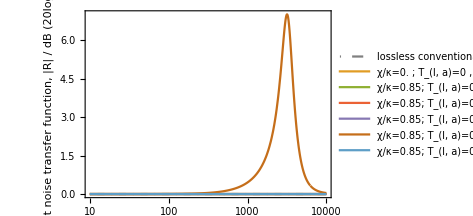
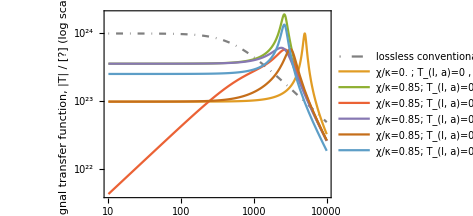
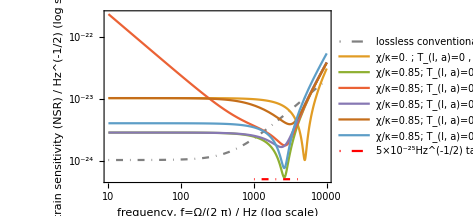

```mathematica
χRatio0=0.85;
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
valsList0={
{0κ,0,0,0,0},
{χRatio0 κ,0,0,0,0},
{χRatio0 κ,0.1,0,0,0},
{χRatio0 κ,0,0.1,0,0},
{χRatio0 κ,0,0,0.1,0},
{χRatio0 κ,0,0,0,0.5}};
plotsWLC[valsList0,"lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects"]
```

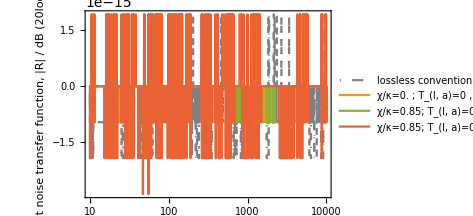
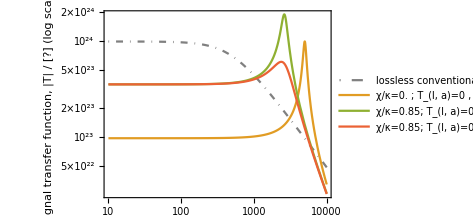
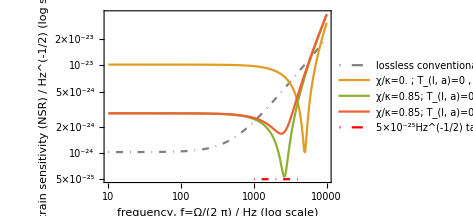

```mathematica
χRatio1=0.85;
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
valsList1={
{0κ,0,0,0,0},
{χRatio0 κ,0,0,0,0},
{χRatio0 κ,0,0.1,0,0}};
plotsWLC[valsList1,"lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects"]
```

```mathematica
(*to-do: manipulate and optimisation need to be reworked for the new plotsWLC[-]*)

(*Manipulate[
plotsWLCPDLossy[{
{0κ,0,0},
{r κ,0,0},
{r κ,0,0.5},
{r κ,0.1,0},
{r κ,0.1,0.5}},"lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects\nconventional detector is lossless"],{{r,0.9},0,1}]*)
```

```mathematica
(*
(*copying μtric0 code from degIntSqz.nb -- to-do: unify workflow and .nb's*)
{f0, f1} = {1 10^3,4 10^3};(*Hz*)
ASDShCrit = 5 10^-25;(*Hz^(-1/2)*)
ShCrit=ASDShCrit^2;(*Hz^-1*)
μtric0[fnSh_]:=1/(f1-f0)NIntegrate[Max[1/fnSh[2π f]-1/ShCrit,0]/(1/ShCrit),{f,f0,f1}]
printμtric0[fnSh_]:=Print[StringForm["For S_h(Ω) given by: ``\n--> μtric0=`` (unitless)",fnSh,NumberForm[μtric0[fnSh]]]]
(*end of copied code*)
reduSh0[Ω_?NumericQ,r_?NumericQ]:=ASDhPDLossy[Ω,r κ,0,0]^2
optiFn0[r_?NumericQ]:=μtric0[reduSh0[#,r]&]
(*because of zeroing of μtric0, optimisation must be run from a non-zero starting value*)
optiVals0=NMaximize[{optiFn0[r],0.9<r<1},r]
printμtric0[ASDhPDLossy[#,(r/.optiVals0[[2]][[1]]) κ,0,0]^2&]
(*optimisation finds a value off threshold -- interesting!*)

-Graphics-;
plotsWLCPDLossy[{
{0κ,0,0},
{(r/.optiVals0[[2]][[1]]) κ,0,0},
{(r/.optiVals0[[2]][[1]]) κ,0,0.5},
{(r/.optiVals0[[2]][[1]]) κ,0.1,0},
{(r/.optiVals0[[2]][[1]]) κ,0.1,0.5}},"lossy optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects\nconventional detector is lossless\nlossless model uses μtric0 optimal result"]
*)
```